```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
(*these are BARE WAVEFUNCTION OVERLAP!!!*)
fcfs=Import["a3sigma_c3sigma.csv"];
```

```mathematica
(*first unbound states*)
fcfs[[26,75]]
(*least bound states*)
fcfs[[25,74]]


(*free ground state atoms to Strong PA line @ -30GHz*)
fcfs[[26,71]]
(*least bound state to Strong PA line @ -30GHz*)
fcfs[[25,71]]
```

0.99992

0.69124

0.0006695

-0.19599

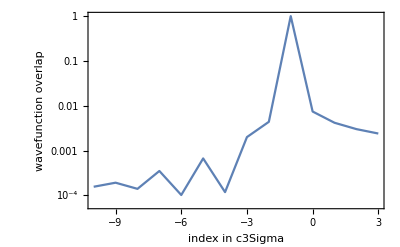

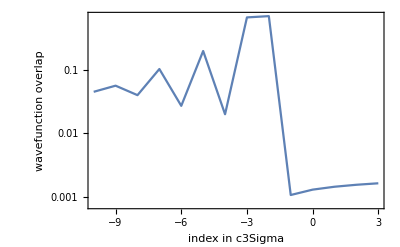

```mathematica
(*71 is -5 in our paper, so 76 is zero*)
index2=Range[Length[fcfs[[1]]]]-76;


upleg=Thread[{index2,Abs[fcfs[[26,;;]]]}];
downleg=Thread[{index2,Abs[fcfs[[25,;;]]]}];
ListLogPlot[upleg[[66;;79]],Joined->True,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"index in c3Sigma","wavefunction overlap","upleg"},LabelStyle->{Large,Black}]
ListLogPlot[downleg[[66;;79]],Joined->True,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"index in c3Sigma","wavefunction overlap","downleg"},LabelStyle->{Large,Black}]
```